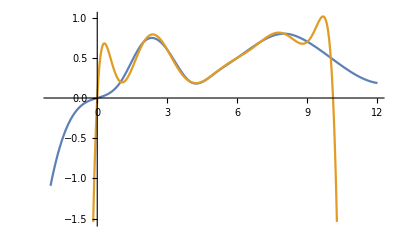

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"../NaturalCubicSpline.m"}]];
Import[FileNameJoin[{NotebookDirectory[],"../LagrangeInterpolatingPolynomial.m"}]];

xval={0,1,2,3,4,5,6,7,8,9,10};
fxval={0,0.2,0.7,0.6,0.2,0.3,0.5,0.7,0.8,0.7,0.5};

NCSEstimator=NaturalCubicSpline[xval,fxval];
LIPEstimator=LagrangeInterpolatingPolynomial[xval,fxval];

Plot[{NCSEstimator[x],LIPEstimator[x]},{x,-2,12}]
```